```mathematica
allelefreq[tot_]:=Block[{w,dd,r1,r2,tottot},
w=Table[tot[[i,2]]+.5tot[[i,3]]+.5tot[[i,4]]+.5tot[[i,5]],{i,Length[tot]}];

dd=Table[tot[[i,6]]+.5tot[[i,3]]+.5tot[[i,7]]+.5tot[[i,8]],{i,Length[tot]}];
r1=Table[tot[[i,9]]+.5tot[[i,4]]+.5tot[[i,7]]+.5tot[[i,10]],{i,Length[tot]}];
r2=Table[tot[[i,11]]+.5tot[[i,5]]+.5tot[[i,8]]+.5tot[[i,10]],{i,Length[tot]}];

tottot=(0.1+Total[Transpose[tot[[All,2;;11]]]]);
biters=(0.1+Total[Transpose[tot[[All,{2,3,4,5,7,9,10}]]]]);
N[{w/tottot,dd/tottot,r1/tottot,r2/tottot,biters/tot[[10,2]]}]];
```

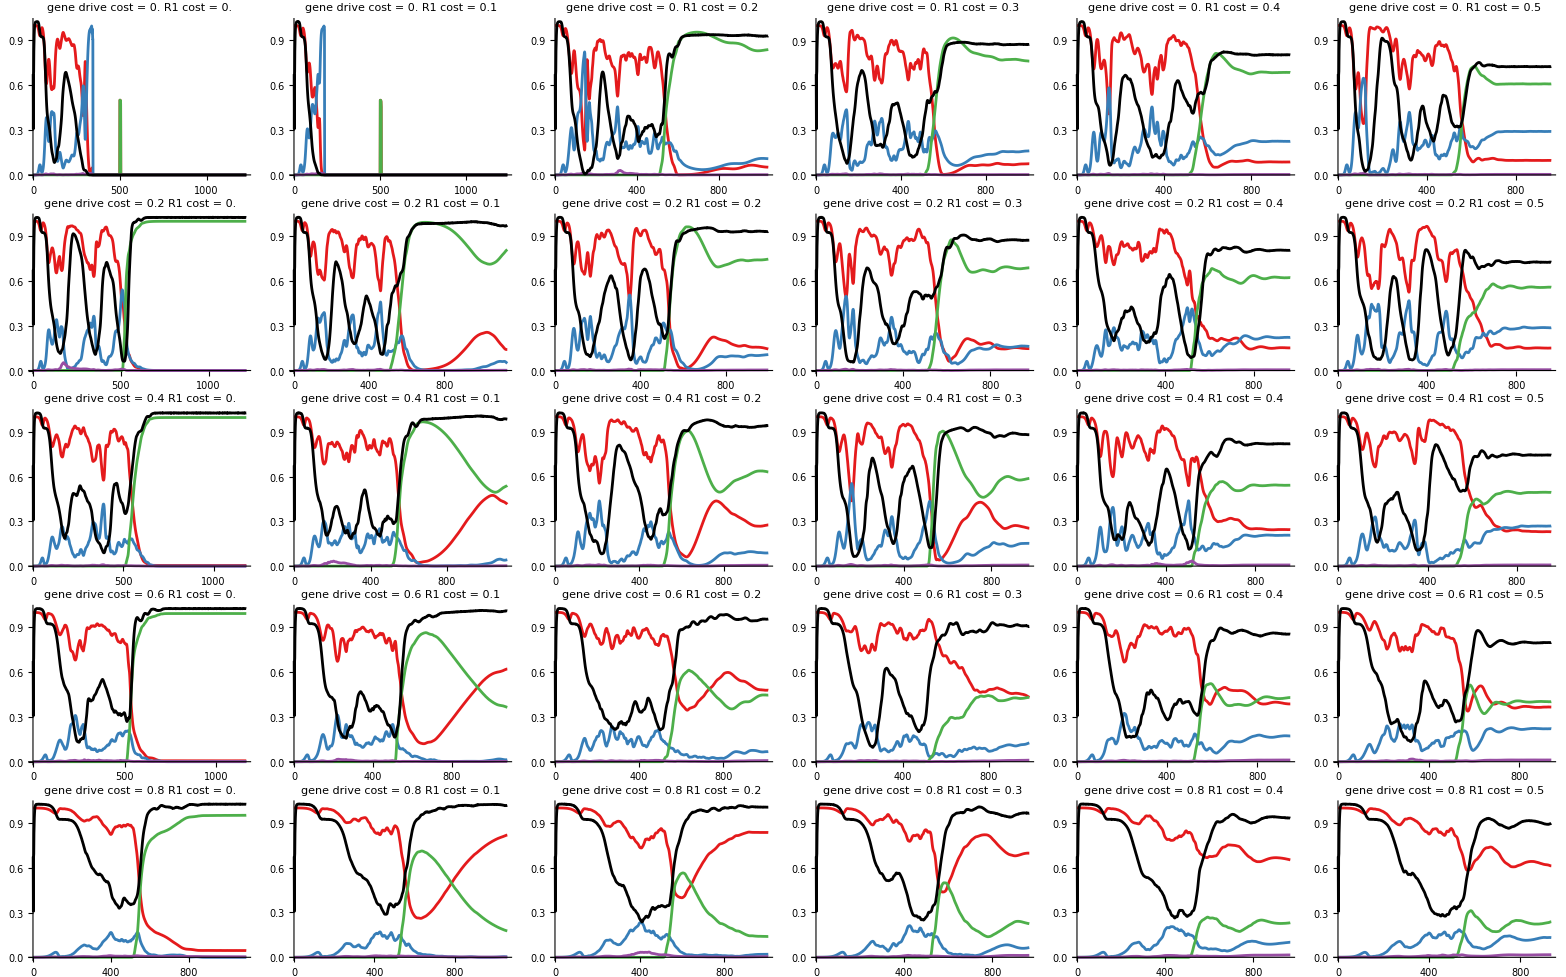

```mathematica
xili=Range[0,0.8,0.2];
mutcostli=Range[0,0.5,0.1];
plots=Table[{},{xx,Length[xili]},{mm,Length[mutcostli]}];
cc={RGBColor[Rational[76, 85], Rational[26, 255], Rational[28, 255]],RGBColor[Rational[11, 51], Rational[42, 85], Rational[184, 255]],RGBColor[Rational[77, 255], Rational[35, 51], Rational[74, 255]],RGBColor[Rational[152, 255], Rational[26, 85], Rational[163, 255]],Black};
SetDirectory["~/Dropbox/Doublesex/Resistance/Evolution/InLocResis/output_files"];
Do[
totals=Drop[Import["Totals"<>ToString[set=100+10 mm+xx]<>"run1.txt","Table"],2];
{ww,dd,r1,r2,rel}=allelefreq[totals];plots[[xx,mm]]=ListLinePlot[{ww,dd,r1,r2,rel},PlotStyle->cc,PlotRange->All,PlotLabel->"gene drive cost = "<>ToString[xili[[xx]]]<>"\nR1 cost = "<>ToString[mutcostli[[mm]]]],{xx,Length[xili]},{mm,Length[mutcostli]}];
Grid[plots]
```